# Efficiency Comparison

## Defining Methods and Preamble

## Preamble

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
```

## Plotting Method

```mathematica
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
RGBColor/@hexColors
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06,modelLabel_:"AE", modelLabelPos_:{0.639,0.899}]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};


nBoxes=Length[data];
q10=Quantile[#,0.10]&/@data;
q90=Quantile[#,0.90]&/@data;
(*x positions in BoxWhiskerChart coordinates*)
xPos=Range[nBoxes];
     p10p90Graphics=Table[{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{xPos[[i]]-0.39,q10[[i]]},{xPos[[i]]+0.39,q90[[i]]}]},{i,nBoxes}];

plot=BoxWhiskerChart[
data,
{"Outliers",
{"MedianMarker",1.0,Directive[RGBColor["#94a4a2"],AbsoluteThickness[3], Opacity[2]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"MeanMarker",0.78,Directive[Black, Opacity[1],AbsoluteThickness[3]]},
{"MeanDiamond",0.8,Directive[RGBColor["#92dadd"], Opacity[0.4]]},
{"Outliers",Graphics[{RGBColor["#3f90da"],Rectangle[{-1,-1},{1,1}]}]}
},
Prolog->p10p90Graphics,
BarSpacing->0.3,
ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.8]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[1.5]],
ImageSize->1300,AspectRatio->0.65,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[-0.03]},{Scaled[0.03],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.165, 0.3,0.43, 0.57};

Graphics[
Join[
{
Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},
Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],
{
Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],
Inset[tevText,Scaled[tevPos],{Right,Bottom}],
Inset[Framed[Style[modelLabel,FontFamily->"TeX Gyre Heros",Italic,32,Black],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],RoundingRadius->0,FrameMargins->{{8,8},{4,4}}],Scaled[modelLabelPos],{Right,Top}]
}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]
```

{RGBColor[0.24705882352941178, 0.5647058823529412, 0.8549019607843137],RGBColor[1., 0.6627450980392157, 0.054901960784313725],RGBColor[0.7411764705882353, 0.12156862745098039, 0.00392156862745098],RGBColor[0.5803921568627451, 0.6431372549019608, 0.6352941176470588],RGBColor[0.5137254901960784, 0.17647058823529413, 0.7137254901960784],RGBColor[0.6627450980392157, 0.4196078431372549, 0.34901960784313724],RGBColor[0.9058823529411765, 0.38823529411764707, 0.],RGBColor[0.7254901960784313, 0.6745098039215687, 0.4392156862745098],RGBColor[0.44313725490196076, 0.4588235294117647, 0.5058823529411764],RGBColor[0.5725490196078431, 0.8549019607843137, 0.8666666666666667]}

## Data Plots

## Efficiency Plot: AE @ 250 Hz

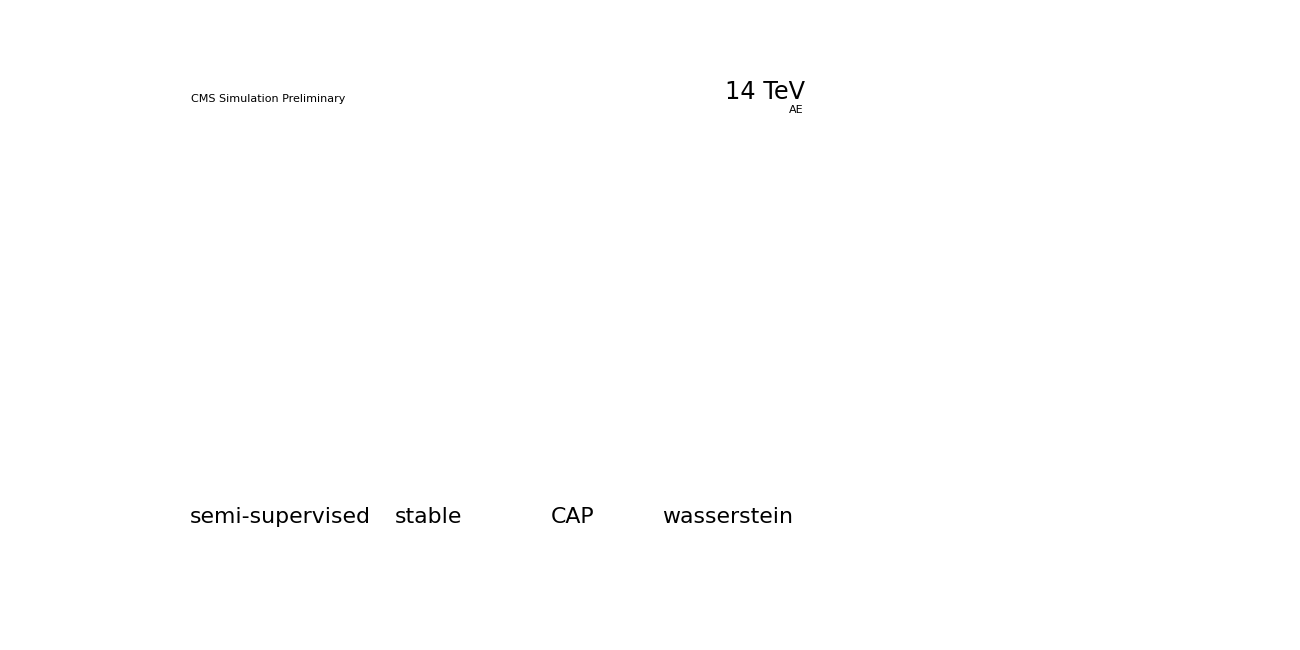

effs/ae_250Hz.svg

effs/ae_250Hz.pdf

effs/ae_250Hz.jpeg

```mathematica
(*Data AE @ 250Hz*)
semisupervised={0.31,0.53,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41};
CAP={0.18,0.44,0.00,0.05,0.98,0.87,0.98,13.67,14.24,18.44,0.82,0.04,14.97,13.93,12.62,3.82,0.36,0.41,1.18,16.67};
stable={2.97,0.39,0.00,0.14,0.81,0.67,0.72,9.52,9.81,14.43,0.62,0.04,12.24,9.46,8.23,2.84,0.29,0.30,0.48,11.91};
wasserstein={0.16,0.22,0.00,0.03,0.77,0.57,0.66,5.38,5.42,14.82,0.51,0.02,12.21,5.47,5.32,2.45,0.20,0.18,0.33,9.64};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: AE @ q99

```mathematica
(*Data AE q99*)
semisupervised={1.57,0.46,0.00,0.17,1.45,0.82,0.77,13.88,14.23,16.41,2.25,0.06,14.49,11.94,12.55,6.80,0.54,0.34,0.57,13.64};
CAP={0.23,0.51,0.00,0.05,1.13,1.01,1.08,14.13,14.87,17.99,0.97,0.05,13.78,14.91,12.79,3.94,0.35,0.41,1.04,17.35};
stable={1.78,0.27,0.00,0.07,0.45,0.54,0.65,8.75,9.10,13.80,0.47,0.03,11.52,8.92,7.21,2.09,0.19,0.15,0.23,10.55};
wasserstein={1.46,0.24,0.00,0.06,0.49,0.53,0.69,8.00,8.27,13.46,0.49,0.02,10.86,8.26,6.74,1.95,0.19,0.21,0.32,10.41};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

## Efficiency Plot: VAE @ 250 Hz

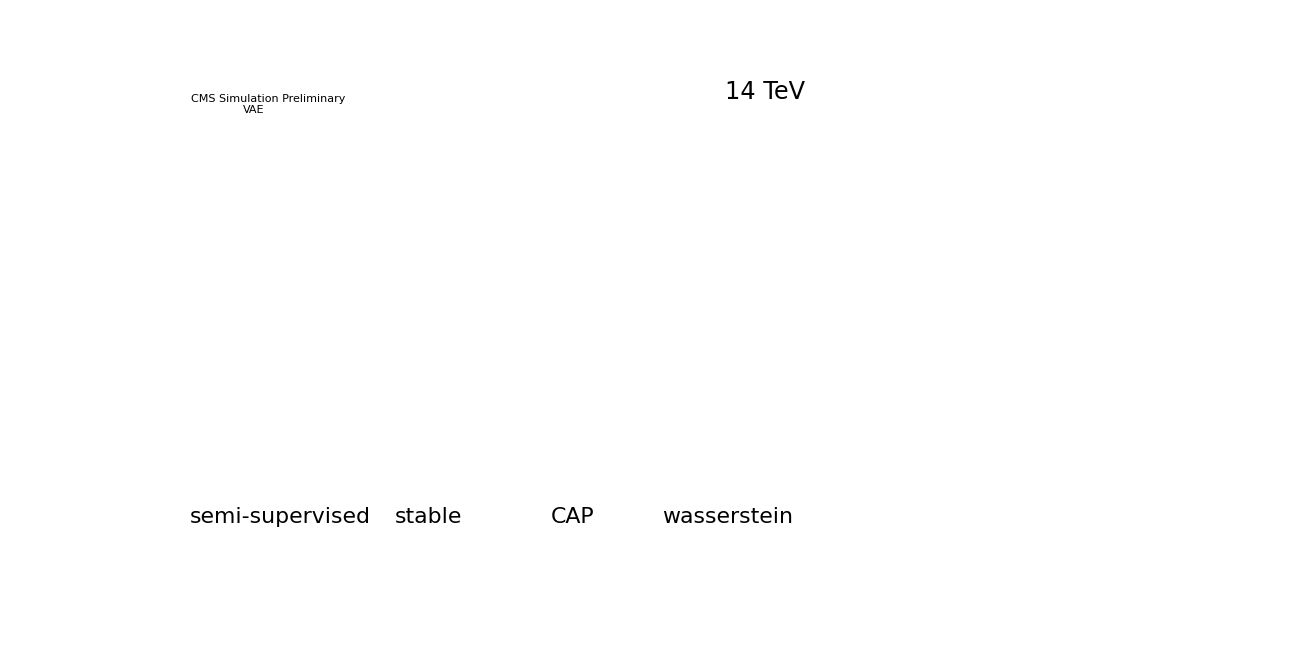

effs/vae_250Hz.svg

effs/vae_250Hz.pdf

effs/vae_250Hz.jpeg

```mathematica
(*Data VAE*)
semisupervised={0.02,0.18,0.00,0.00,0.77,0.86,1.02,8.43,8.88,18.93,0.68,0.04,12.44,10.11,9.15,2.79,0.32,0.24,0.38,15.93};
CAP={0.02,0.20,0.00,0.00,0.82,0.93,1.10,8.87,9.35,19.74,0.73,0.04,12.93,10.70,9.60,2.93,0.32,0.24,0.40,16.83};
stable={0.02,0.19,0.00,0.01,0.95,1.03,1.15,6.34,6.56,21.12,0.65,0.04,15.36,8.08,7.14,2.34,0.33,0.21,0.36,15.90};
wasserstein={0.02,0.21,0.00,0.01,0.91,1.07,1.17,5.77,5.92,23.70,0.78,0.04,15.10,7.62,6.77,2.76,0.32,0.12,0.18,17.37};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"VAE", {0.151, 0.899}]
Export["effs/" <> "vae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_250Hz" <>".jpeg",plot,"JPEG"]
```

```mathematica
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
```

## Efficiency Plot: VAE @ q99

```mathematica
(*Data VAE q99*)
semisupervised={0.08,0.17,0.00,0.02,1.14,0.96,1.05,7.85,8.05,20.03,0.67,0.04,15.29,9.11,8.09,2.96,0.36,0.33,0.67,14.90};
CAP={0.05,0.18,0.00,0.01,1.13,0.99,1.12,7.54,7.81,18.99,0.69,0.03,14.50,8.65,8.34,2.83,0.37,0.58,1.07,15.13};
stable={0.02,0.17,0.00,0.01,0.97,1.07,1.17,6.43,6.59,19.48,0.66,0.03,14.75,8.05,6.97,2.54,0.29,0.11,0.18,15.86};
wasserstein={0.02,0.21,0.00,0.01,0.91,1.06,1.16,5.76,5.91,23.59,0.76,0.04,15.02,7.59,6.75,2.75,0.32,0.12,0.18,17.27};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "VAE",{0.151, 0.899}]
Export["effs/" <> "vae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/vae_q99.svg

effs/vae_q99.pdf

effs/vae_q99.jpeg

## Efficiency Plot: DS AE @ 250 Hz

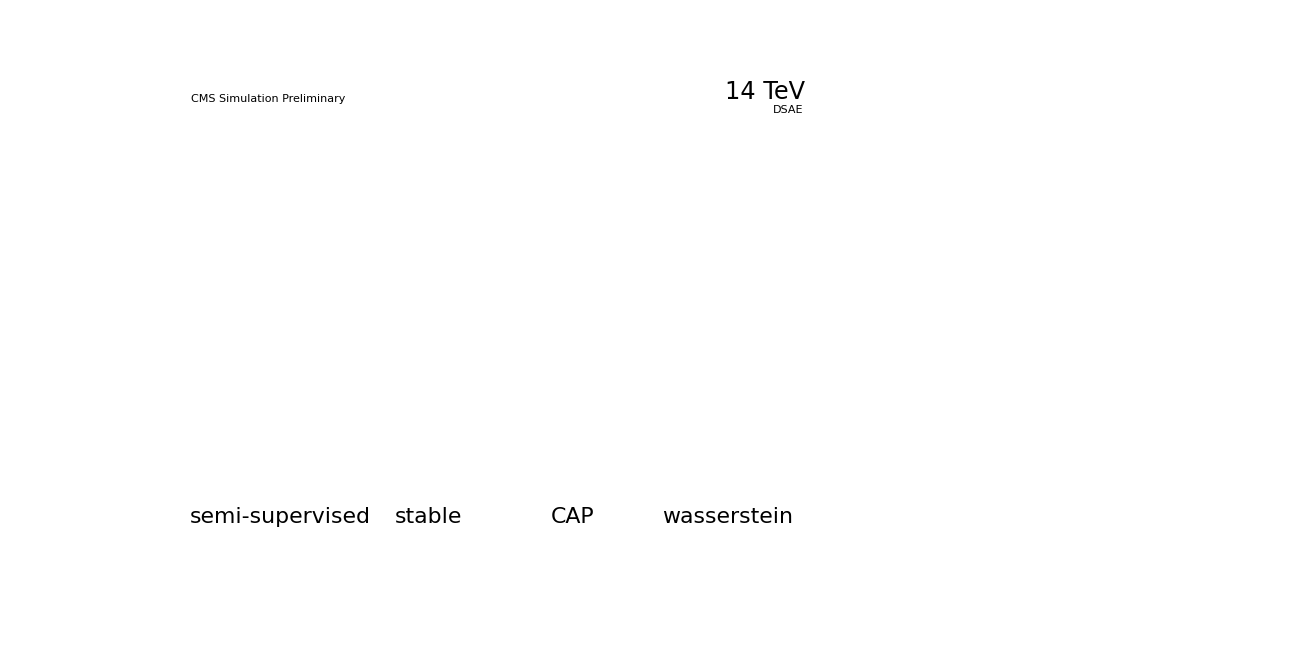

effs/dsae_250Hz.svg

effs/dsae_250Hz.pdf

effs/dsae_250Hz.jpeg

```mathematica
(*Data DS AE*)
semisupervised={0.47,0.59,0.00,0.10,1.22,1.04,1.16,24.23,25.34,17.00,1.16,0.05,13.27,21.69,21.13,6.43,0.40,0.60,1.00,19.04};
CAP={0.39,0.61,0.00,0.10,1.23,1.08,1.20,26.20,26.86,20.58,1.12,0.05,15.23,23.61,23.15,6.91,0.43,0.68,1.12,20.36};
stable={1.01,0.33,0.00,0.04,0.86,0.56,0.68,6.52,6.58,14.04,0.60,0.02,11.11,5.88,6.23,2.13,0.26,0.73,4.65,9.09};
wasserstein={0.15,1.74,0.00,0.02,1.04,0.72,0.84,6.25,6.60,15.32,0.66,0.03,12.84,6.37,6.33,2.67,0.31,0.47,1.36,11.24};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSAE", {0.639, 0.899}]
Export["effs/" <> "dsae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency plot: DS VAE @ 250 Hz

{0.02,0.19,0.,0.01,1.1,1.02,1.15,9.51,10.,19.45,0.7,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87}

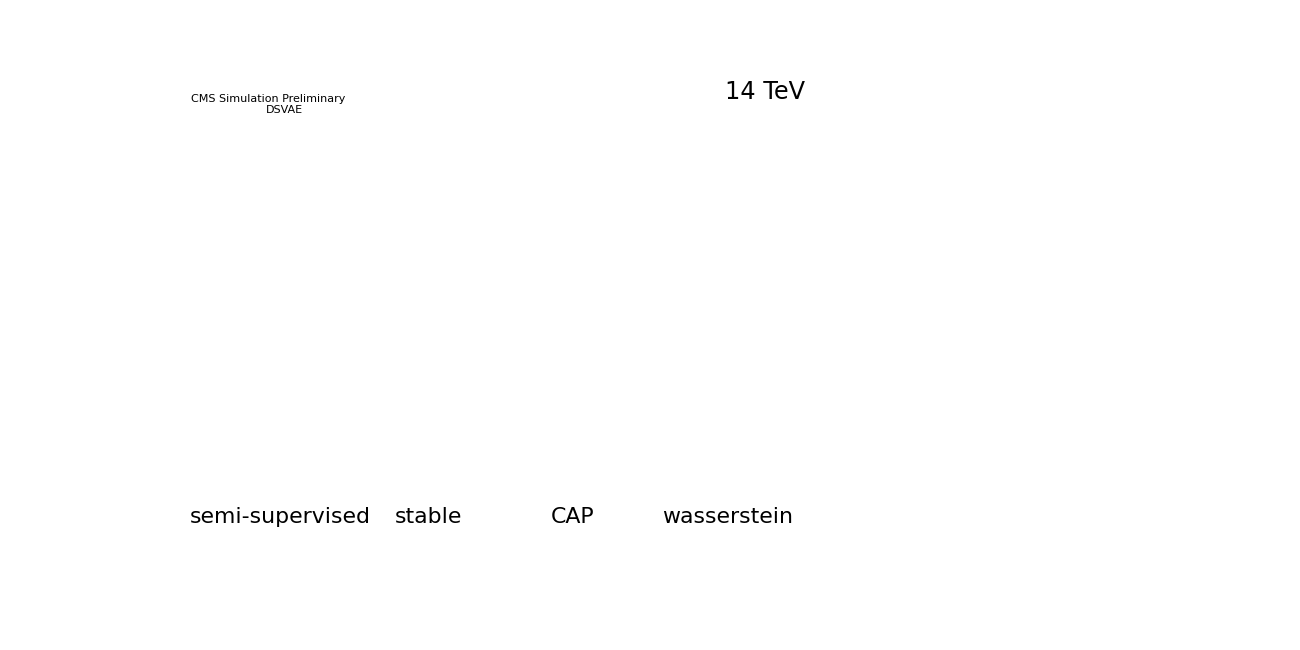

effs/dsvae_250Hz.svg

effs/dsvae_250Hz.pdf

effs/dsvae_250Hz.jpeg

```mathematica
(*Data DS VAE*)
semisupervised={0.11,0.18,0.00,0.01,1.18,0.97,1.12,12.13,12.89,17.85,0.77,0.04,14.00,13.12,11.79,3.63,0.38,0.44,0.76,16.27};
CAP={0.02,0.19,0.00,0.01,1.10,1.02,1.15,9.51,10.00,19.45,0.70,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87}
stable={0.03,0.16,0.00,0.00,1.08,1.01,1.12,9.34,9.63,19.14,0.79,0.04,13.95,10.75,10.00,3.29,0.38,0.40,0.72,16.10};
wasserstein={0.02,0.71,0.00,0.01,0.85,1.00,1.18,8.64,9.30,20.43,0.99,0.04,12.65,10.30,8.67,2.95,0.29,0.20,0.32,16.36};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSVAE", {0.186, 0.899}]
Export["effs/" <> "dsvae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsvae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsvae_250Hz" <>".jpeg",plot,"JPEG"]
```